# Machine learning for potion development at Hogwarts

ORIGINAL ARTICLE: Christoph F. Kurz and Adriana N. König. Machine learning for potion development at Hogwarts. arXiv:2307.00036 (2023).
DOI: https://doi.org/10.48550/arXiv.2307.00036

In the world of Harry Potter, potions are magical drinks that can do amazing things, like changing your appearance or making you lucky. But making potions is not easy. You need special equipment, ingredients, and skills. Even a tiny mistake can ruin your potion or cause an accident. Just ask Neville Longbottom, who got boils all over his face in class.

At Hogwarts, students learn how to brew potions from the first to the fifth year. If they are good enough, they can continue studying potions in their sixth and seventh years. Some of the best potion makers in history are Professor Snape, who taught potions at Hogwarts for many years, and Harry Potter, who followed some secret tips in his textbook .

But what if there was a way to create new potions without risking explosions or poisoning? What if we could use artificial intelligence (AI) to help us? AI is a branch of computer science that can learn from data and solve problems. It has been used for many things, like finding new drugs or designing molecules.

In this work, we use AI to generate recipes for magic potions. We use a neural network, which is a type of AI that can learn from examples, to predict what effect a potion will have based on its ingredients. We also use a random generator to create new combinations of ingredients that have never been used before. We hope that this will help us discover new and exciting potions that can benefit the wizarding world.

## Data Import

First, we import the data. We collected all recipes from various Harry Potter fan sites and wikis and classified them
according to the Anatomical Therapeutic Chemical (ATC) classification system:

```mathematica
dataClean=Import["https://raw.githubusercontent.com/krz/hp-potion-discovery/main/hp_potions.wl"]
```

## Model Development

### Load the Pre-trained Model

Load the BioBERT model. This language model has been pre-trained on large-scale biomedical corpora comprising over 18
billion words from PubMed abstracts and full-text articles.

```mathematica
sentenceembedding=NetAppend[NetModel["BioBERT Trained on PubMed and PMC Data"],"last"->SequenceLastLayer[]]
```

NetChain[<>]

How many recipes belong to each class:

```mathematica
Counts@Values[dataClean]//Dataset
```

### Finetuning of the Model

Build embeddings on training data

```mathematica
trainembeddings=sentenceembedding[dataClean[[All,1]],TargetDevice->"CPU"]->dataClean[[All,2]];
```

Add a new Softmax layer for classification

```mathematica
classifierhead=NetChain[{DropoutLayer[],11,SoftmaxLayer[]},"Output"->NetDecoder[{"Class",{"dermatologicals","psychoanaleptics","poison","anesthetics","various","musculo-skeletal system","antiparasitic products, insecticides and repellents","antiinfectives for systemic use","psycholeptics","sensory organs","respiratory system"}}]]
```

NetChain[<>]

### Model Training

Train the model on the recipes

```mathematica
bertresults=NetTrain[classifierhead,trainembeddings,TargetDevice->"CPU",MaxTrainingRounds->2000]
```

NetChain[<>]

Show an example recipe

```mathematica
data[[1,1]]
```

Add crushed snake fangs to your cauldron and stir.
Slice your Pungous Onions finely and place in cauldron, then heat the mixture.
Add dried nettles. Add a dash of Flobberworm Mucus and stir vigorously.
Add a sprinkle of powdered ginger root and stir vigorously again.
Add pickled Shrake spines. Stir gently, so as not to overexcite the Shrake spines.
Add a glug of stewed horned slugs. Add porcupine quills. Finally, wave your wand over the cauldron to finish the potion.

### Generate New Recipes

Generate new recipes with between 3 and 8 individual steps

```mathematica
sentences=StringJoin@Keys[dataClean];
```

```mathematica
genSentences[]:=Module[{sen=StringJoin[StringJoin[#,"."]&/@RandomSample[StringSplit[sentences,"."], RandomInteger[{3,8}]]]},{sen,bertresults[sentenceembedding[sen],{"TopProbabilities",1}]}]
```

Generate example recipe and classify it

```mathematica
genSentences[]
```

{ Add five sliced caterpillars. Allow to simmer until the potion turns purple. Add 2 measures of Standard Ingredient to the mortar. Add Baneberry. Add three flying seahorses. Stirring Simmering lowers heat. Add Wormwood. Add the ground unicorn horn until it turns turquoise.,{psychoanaleptics→0.996987}}

Generate 10000 random recipes and classify them (this takes ~40min)

```mathematica
SeedRandom[34231];res=Table[{genSentences[]},10000];
```

Flatten results

```mathematica
resFlat=Flatten[res[[All,All,2]],1];
```

## Results

Most of the 10, 000 generated recipes fall into the psychoanaleptics category (n = 5549), followed by the dermatologicals
category (n = 1539) and the various category (n = 1487). 225 recipes fall into the poison category.

Figure 1: Predicted potion categories of the 10000 randomly generated recipes

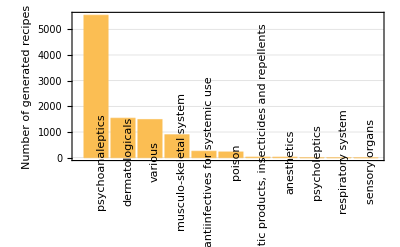

```mathematica
BarChart[<|ReverseSort@Counts@Keys@Flatten@Normal@resFlat|>,ChartLabels->Placed[Keys@ReverseSort@Counts@Keys@Flatten@resFlat,Below,Rotate[#,90Degree]&],PlotTheme->"Detailed",FrameLabel->{None,"Number of generated recipes"}]
```

```mathematica
ReverseSort@Counts@Keys@Flatten@resFlat
```

<|psychoanaleptics→5549,dermatologicals→1539,various→1487,musculo-skeletal system→896,antiinfectives for systemic use→253,poison→225,antiparasitic products, insecticides and repellents→23,anesthetics→21,psycholeptics→3,respiratory system→3,sensory organs→1|>

Predicted probabilities of belonging to a certain ATC category were often above 90%.

Figure 2: Histogram of the predicted probabilities

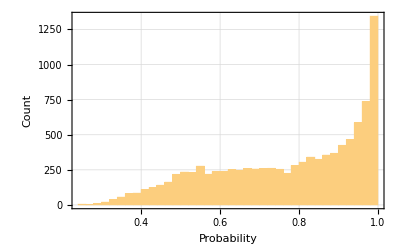

```mathematica
Histogram[Values@Flatten@resFlat,50,"Count",PlotTheme->"Detailed",FrameLabel->{"Probability","Count"}]
```

Some example recipes and their classification results:

```mathematica
bertresults[sentenceembedding["Add Baneberry. Add 2 bundles of knotgrass to the cauldron. Add Dogbane. Add syrup of hellebore until the
potion turns turquoise. Add a sprig of Peppermint to counteract side-effects. Add Honey water until it turns
back to a turquoise colour. Stir four times anti-clockwise. Add the Infusion of Wormwood."],{"TopProbabilities",3}]
```

{musculo-skeletal system→0.00018395,various→0.000304334,psychoanaleptics→0.99944}

```mathematica
bertresults[sentenceembedding["Add Stewed Mandrake. Add Wormwood. Add a dash of Flobberworm Mucus and stir vigorously. Leave to brew
and return in 8 hours (Copper), 14 hours (Brass), or 23 hours (Pewter). Shake and add wormwood until the potion
turns green. Slice bursting mushrooms with knife, add to cauldron and stir clockwise until potion turns blue."],{"TopProbabilities",3}]
```

{psychoanaleptics→0.104831,antiinfectives for systemic use→0.241033,dermatologicals→0.583635}

## Conclusion

We used AI to create new potion recipes for Hogwarts. We found many new ways to mix ingredients and stir them to get different effects. AI can also help us find good or bad combinations of drugs or potions. But AI is not perfect. It needs a lot of data, and potions can be very different even in the same category. Also, AI can be dangerous if used for evil purposes. Imagine if someone made a potion stronger than anything Lord Voldemort ever used! And we are just muggles, so we don’t know how well our potions really work.